# Basic conventions for graphs

Ileana Streinu
CSC 253 Spring 2022

## Basic conventions for our Graphs

1. Vertices : labeled consecutively from 0 to n - 1, where n is the number of vertices
2. Edges: are pairs between vertices (i.e. pairs of numbers between 0 and n-1)

## Examples

### Correct

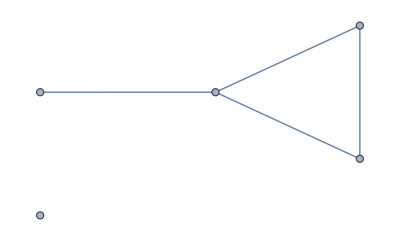

```mathematica
GRAPH01=Graph[{0,1,2,3,4},{0<->2,2<->3,3<->0,0<->4}]
```

```mathematica
GRAPH02=Graph[{},{}]
```

-Graphics-

```mathematica
GRAPH03=Graph[{0,1,2},{}]
```

-Graphics-

### Incorrect

```mathematica
GRAPH04=Graph[{0,2,5},{}]
```

-Graphics-

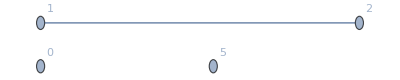

```mathematica
GRAPH05=Graph[{0,2,5},{1<->2},VertexLabels->Automatic]
```